## grupa 1

#### Zad. 1

```mathematica
f=3 x^7-2/x^6+4 x^(1/3);
g=(3^x+Cos[x])/(Sin[x]+Log[x]);
h=Sin[x^3] Sin[x]^3;
D[f,x]
D[g,x]//Simplify
D[h,x]//Simplify
```

12/x^7+4/(3 x^(2/3))+21 x^6

(-(3^x+Cos[x]) (1/x+Cos[x])+(3^x Log[3]-Sin[x]) (Log[x]+Sin[x]))/(Log[x]+Sin[x])^2

3 Sin[x]^2 (x^2 Cos[x^3] Sin[x]+Cos[x] Sin[x^3])

#### Zad. 2

```mathematica
F[x_]:=(2x)/(x+1);
F'[x]//Simplify
F''[x]//Simplify
Series[F[x],{x,1,2}]
Normal[%]//Expand
F[0.9]
%%/.{x->0.9}
```

2/(1+x)^2

-4/(1+x)^3

1+(x-1)/2-1/4 (x-1)^2+O[x-1]^3

1/4+x-x^2/4

0.947368

0.9475

#### Zad. 3

-(2 (-2+x) (-1+2 x))/((-1+x)^2 (1+x)^2)

-2 (-2+x) (-1+2 x)

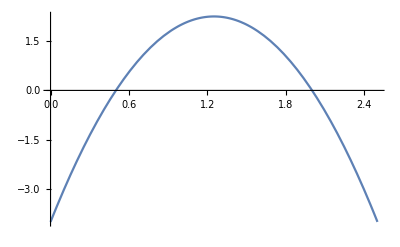

```mathematica
f1=(4x-5)/(-1+x^2);
D[f1,x]//Factor
Numerator[%]
Plot[%,{x,0,2.5}]
```

## grupa I1

#### Zad. 1

```mathematica
f=4 x^8-5/x^10+10/((x^2)^(1/3));
g=(Tan[x]+2Log[x])/(3ArcTan[x]+2Sin[x]);
h=Log[Cos[Log[x]]];
D[f,x]
D[g,x]//Simplify
D[h,x]//Simplify
```

50/x^11+32 x^7-(20 x)/(3 (x^2)^(4/3))

((2/x+Sec[x]^2) (3 ArcTan[x]+2 Sin[x])-(3/(1+x^2)+2 Cos[x]) (2 Log[x]+Tan[x]))/(3 ArcTan[x]+2 Sin[x])^2

-Tan[Log[x]]/x

#### Zad. 2

```mathematica
F[x_]:=Sqrt[1+x];
F'[x]//Simplify
F''[x]//Simplify
Series[F[x],{x,0,2}]
Normal[%]//Expand
F[0.1]
%%/.{x->0.1}
```

1/(2 √(1+x))

-1/(4 (1+x)^(3/2))

1+x/2-x^2/8+O[x]^3

1+x/2-x^2/8

1.04881

1.04875

#### Zad. 3

ⅇ^(-x^2) x^3

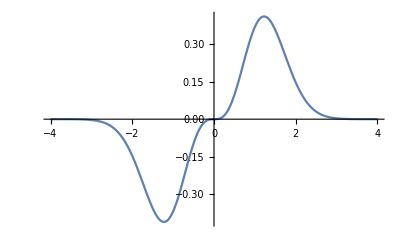

```mathematica
x^3 Exp[-x^2]
Plot[%,{x,-4,4}]
```

-2 ⅇ^(-x^2) x^3 (-2+x^2)

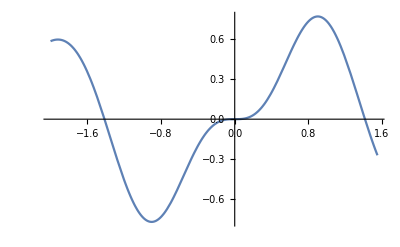

```mathematica
f1=x^4 Exp[-x^2];
D[f1,x]//Factor
Plot[%,{x,-2,1.55}]
```